```mathematica
ClearAll["Global`*"]
SetDirectory["/Volumes/Apollo/2020/Ultralearning/CFD/"];
Get[ "/Volumes/Apollo/2020/Ultralearning/CFD/functions.m"]

(*Rey= 1000; (*Reynolds Number*)*)
Reynolds = List[1,10,100,1000,5000,10000];
(*Inteirior Points*)
imax = 10; (*Number of Cell in X direction *)
jmax = 10; (*Number of Cell in Y direction *)
xlength =1;
ylenght =1;
delx = 1/(imax);(* Spatial step interval in X direction *)
dely = 1/(jmax); (* Spatial step interval in Y direction *)
ustar=1; (* normalized velocity of lid *)
(* Time conditions *)
(* Initialize time value and time index *) 

delt = 0.02;  (*Time Step*)
tau = 0.5; (*Safety factor for time step size control τ*)
tend=3.8;

(*Pressure Itertion Data *)
it = 0;(* SOR counter  *)
res = 0;  (* Norm of pressure equation residual*)
eps = 0.001; (* Stopping tolerance for pressure iteration*)
gamma = 0.9;(*Upwind differencing factor γ*)

(*Problem Dependent quatities *)

GX = 0;(* Body forces *)
GY= 0;(* Body forces *)
UI = 0;  (* Initial Velocity *)
VI =0; (* Initial Velocity *)
PI = 0; (* Initial Pressure *)
Umed = 1; (*Mean velocity Value of the lid *)
itermax=100;(* Max iteration in SOR *)
omega=1.7;(* SOR Relaxation*)
TOL=0.001;(* SOR Tolerance*)

P= Table[0,{imax+2},{jmax+2}] ;(* Pressure *)
wW=2;wE=2;wN=2;wS=2; (*flags to indicate no slip condition on a wall *)

(*Saving info*)
SU= Table[U,4*Round[tend]];
SV=Table[V,4*Round[tend]];

(*Saving Reynolds info info*)
RU= Table[U,Length[Reynolds]];
RV=Table[V,Length[Reynolds]];

(*F= Table[0,{imax+2},{jmax+2}]; (* F *)
G= Table[0,{imax+2},{jmax+2}]; (* G *)*)
GSV=Table[0,{(imax)*(jmax)}];(*Vector initialization for gauss seidel*)


For[l=1,l<=6,l++,

U = Table[0,{imax+2},{jmax+2}];(* Velocity in x-direction *)
V = Table[0,{imax+2},{jmax+2}];(* Velocity in y-direction *)

timet=0;timen=0;(* timet:time value,timen:time index *)

(*Data Array Initialization *)
     (*initialize and assign initial values to u,v,and p*)

(*Boundary Correction*)
    (*U[[All,jmax+2 ]]=2*Umed-U[[All,jmax+1]] ;(*CORRECT THIS *)
U[[1,jmax+2]]=0.0; (*@ the wall *)
U[[imax+2,jmax+2]]=0.0; (* @ the wall *)*)
U=boundaryValuesU[U,ustar,imax,jmax,wN,wE,wW,wS];
V=boundaryValuesV[V,imax,jmax,wN,wE,wW,wS];
(* compute F and G according to Eqs.(3.36) and (3.37) *)
     (* compute (d^2 u/d x^2) *)
d2ux = deriv2ux[U,imax,jmax,delx];
(* compute (d^2 u/d y^2) *)
d2uy = deriv2uy[U,imax,jmax,dely];
(* compute (d u^2/d x) *)
d1u2x=deriv1u2x[U,imax,jmax,delx, gamma];
(* compute (d uv/d y) *)
d1uvy=deriv1uvy[U,V,imax,jmax,dely,gamma];
(* compute (d^2 v/d x^2) *)
d2vx=deriv2vx[V,imax,jmax,delx];
(* compute (d^2 v/d y^2) *)
d2vy=deriv2vy[V,imax,jmax,dely];
(* compute (d v^2/d y) *)
d1v2y=deriv1v2y[V,imax,jmax,dely,gamma];
(* compute (d uv/d x) *)
d1uvx=deriv1uvx[U,V,imax,jmax,delx,gamma];

     (* compute F and G *)
F=compF[U,imax,jmax,delx,delt,Reynolds[[l]],GX,d2ux,d2uy,d1u2x,d1uvy];
G= compG[V,imax,jmax,dely,delt,Reynolds[[l]],GY,d2vx,d2vy,d1uvx,d1v2y];

(* compute right-hand size of the pressure Eq.(3.38) *)
RHS=computeRHS[imax,jmax,delt,delx,dely,F,G];
    (*Perform SOR*)
iter=0; (* index for iterative SOR *)
ritnorm=1;  (* tolerance (at first,it is set a large number) *)

Print["---------------------------   ####$#$#### ---------------------------"];
While[ (iter<itermax && ritnorm>eps),
(* compute p of the next step, pNew *)
pNew = computepNew[imax,jmax,omega,delx,dely,P,RHS];
(* compute residual for pressure Eq.according to Eq.(3.45) *)
rit = computeRit[imax,jmax,delx,dely,P,RHS];
(* compute L^2 norm of residual according to Eq.(3.46) *)
ritnorm=Norm[rit,Frobenius]/(imax*jmax);
(* update p *)
P=pNew;
(* increment counter *)
iter=iter+1; 
];
(* compute u and v of the next step according to Eqs.(3.34) and (3.35) *)
U=computeU[U,imax,jmax,delt,delx,F,P];
V=computeV[V,imax,jmax,delt,dely,G,P].00;
timet=timet+delt;

timen=timen+1;
k=1; (*to save info after each time iteration*)
 (* iterations after 1st iteration are written below *)

While[ timet < tend,
(*  select delta t according Eq.(3.50) after 1st time step *)
delt=selectDelta[tau,Reynolds[[l]],delx,dely,U,V];
(* set boundary values for velocity u and v*)
U=boundaryValuesU[U,ustar,imax,jmax,wN,wE,wW,wS];
V=boundaryValuesV[V,imax,jmax,wN,wE,wW,wS];
(* compute F and G according to Eqs.(3.36) and (3.37) *)
(* compute (d^2 u/d x^2) *)
d2ux = deriv2ux[U,imax,jmax,delx];
(* compute (d^2 u/d y^2) *)
d2uy = deriv2uy[U,imax,jmax,dely];
(* compute (d u^2/d x) *)
d1u2x=deriv1u2x[U,imax,jmax,delx, gamma];
(* compute (d uv/d y) *)
d1uvy=deriv1uvy[U,V,imax,jmax,dely,gamma];
(* compute (d^2 v/d x^2) *)
d2vx=deriv2vx[V,imax,jmax,delx];
(* compute (d^2 v/d y^2) *)
d2vy=deriv2vy[V,imax,jmax,dely];
(* compute (d v^2/d y) *)
d1v2y=deriv1v2y[V,imax,jmax,dely,gamma];
(* compute (d uv/d x) *)
d1uvx=deriv1uvx[U,V,imax,jmax,delx,gamma];

(* set boundary values for pressure p,and F and G *)
P = boundaryValuesP[P,imax,jmax,wN,wE,wW,wS];
F=boundaryValuesF[U,imax,jmax,wN,wE,wW,wS];
G = boundaryValuesG[V,imax,jmax,wN,wE,wW,wS];

(* compute F and G *)
F=compF[U,imax,jmax,delx,delt,Reynolds[[l]],GX,d2ux,d2uy,d1u2x,d1uvy];
G= compG[V,imax,jmax,dely,delt,Reynolds[[l]],GY,d2vx,d2vy,d1uvx,d1v2y];

(* compute right-hand size of the pressure Eq.(3.38) *)
RHS=computeRHS[imax,jmax,delt,delx,dely,F,G];

(*Perform SOR*)
ritnorm=1;  (* tolerance (at first,it is set a large number) *)

While[ (iter<itermax && ritnorm>eps),
	(* compute p of the next step, pNew *)
	pNew = computepNew[imax,jmax,omega,delx,dely,P,RHS];
	(* compute residual for pressure Eq.according to Eq.(3.45) *)
	rit = computeRit[imax,jmax,delx,dely,P,RHS];
	(* compute L^2 norm of residual according to Eq.(3.46) *)
	        ritnorm=Norm[rit,Frobenius]/(imax*jmax);
	(* update p *)
	P=pNew;
	(* increment counter *)
	iter=iter+1;
	];

U=computeU[U,imax,jmax,delt,delx,F,P];
V=computeV[V,imax,jmax,delt,dely,G,P].00;
(* Prints Values after 10 iterations *)
If[QuotientRemainder[timen,200][[2]]==0,Print["it# = " ,timen, " timet = ",timet ]];

(* For a videoclip saving info every second*)
(*If[(timet<k/4&&k/4≤timet+delt),
SU[[k]]=U;SV[[k]]=V;
Print["Simulating at ",N[k/4], " seconds currently ..."];
k++;
];*)

(*increment counter*)
timet=timet+delt;
timen++;

];

(*Saving the info for different Reynolds Numbers*)

Print["******************************************************************************"];
Print["************** Restarting the simulation for new Reynolds number **************"];
Print["******************************************************************************"];
RU[[l]]=U;
RV[[l]]=V;
iter=0; (* index for iterative SOR *)

];
```

------------   ####$#$#### ---------------------------

it# = 200 timet = 0.044292

it# = 400 timet = 0.0687061

it# = 600 timet = 0.0931201

it# = 800 timet = 0.117534

it# = 1000 timet = 0.141948

it# = 1200 timet = 0.166362

it# = 1400 timet = 0.190776

it# = 1600 timet = 0.21519

it# = 1800 timet = 0.239604

it# = 2000 timet = 0.264019

it# = 2200 timet = 0.288433

it# = 2400 timet = 0.312847

it# = 2600 timet = 0.337261

it# = 2800 timet = 0.361675

it# = 3000 timet = 0.386089

it# = 3200 timet = 0.410503

it# = 3400 timet = 0.434917

it# = 3600 timet = 0.459331

it# = 3800 timet = 0.483745

it# = 4000 timet = 0.508159

it# = 4200 timet = 0.532573

it# = 4400 timet = 0.556987

it# = 4600 timet = 0.581401

it# = 4800 timet = 0.605815

it# = 5000 timet = 0.630229

it# = 5200 timet = 0.654644

it# = 5400 timet = 0.679058

it# = 5600 timet = 0.703472

it# = 5800 timet = 0.727886

it# = 6000 timet = 0.7523

it# = 6200 timet = 0.776714

it# = 6400 timet = 0.801128

it# = 6600 timet = 0.825542

it# = 6800 timet = 0.849956

it# = 7000 timet = 0.87437

it# = 7200 timet = 0.898784

it# = 7400 timet = 0.923198

it# = 7600 timet = 0.947612

it# = 7800 timet = 0.972026

it# = 8000 timet = 0.99644

it# = 8200 timet = 1.02085

it# = 8400 timet = 1.04527

it# = 8600 timet = 1.06968

it# = 8800 timet = 1.0941

it# = 9000 timet = 1.11851

it# = 9200 timet = 1.14292

it# = 9400 timet = 1.16734

it# = 9600 timet = 1.19175

it# = 9800 timet = 1.21617

it# = 10000 timet = 1.24058

it# = 10200 timet = 1.265

it# = 10400 timet = 1.28941

it# = 10600 timet = 1.31382

it# = 10800 timet = 1.33824

it# = 11000 timet = 1.36265

it# = 11200 timet = 1.38707

it# = 11400 timet = 1.41148

it# = 11600 timet = 1.43589

it# = 11800 timet = 1.46031

it# = 12000 timet = 1.48472

it# = 12200 timet = 1.50914

it# = 12400 timet = 1.53355

it# = 12600 timet = 1.55796

it# = 12800 timet = 1.58238

it# = 13000 timet = 1.60679

it# = 13200 timet = 1.63121

it# = 13400 timet = 1.65562

it# = 13600 timet = 1.68003

it# = 13800 timet = 1.70445

it# = 14000 timet = 1.72886

it# = 14200 timet = 1.75328

it# = 14400 timet = 1.77769

it# = 14600 timet = 1.8021

it# = 14800 timet = 1.82652

it# = 15000 timet = 1.85093

it# = 15200 timet = 1.87535

it# = 15400 timet = 1.89976

it# = 15600 timet = 1.92417

it# = 15800 timet = 1.94859

it# = 16000 timet = 1.973

it# = 16200 timet = 1.99742

it# = 16400 timet = 2.02183

it# = 16600 timet = 2.04625

it# = 16800 timet = 2.07066

it# = 17000 timet = 2.09507

it# = 17200 timet = 2.11949

it# = 17400 timet = 2.1439

it# = 17600 timet = 2.16832

it# = 17800 timet = 2.19273

it# = 18000 timet = 2.21714

it# = 18200 timet = 2.24156

it# = 18400 timet = 2.26597

it# = 18600 timet = 2.29039

it# = 18800 timet = 2.3148

it# = 19000 timet = 2.33921

it# = 19200 timet = 2.36363

it# = 19400 timet = 2.38804

it# = 19600 timet = 2.41246

it# = 19800 timet = 2.43687

it# = 20000 timet = 2.46128

it# = 20200 timet = 2.4857

it# = 20400 timet = 2.51011

it# = 20600 timet = 2.53453

it# = 20800 timet = 2.55894

it# = 21000 timet = 2.58335

it# = 21200 timet = 2.60777

it# = 21400 timet = 2.63218

it# = 21600 timet = 2.6566

it# = 21800 timet = 2.68101

it# = 22000 timet = 2.70542

it# = 22200 timet = 2.72984

it# = 22400 timet = 2.75425

it# = 22600 timet = 2.77867

it# = 22800 timet = 2.80308

it# = 23000 timet = 2.8275

it# = 23200 timet = 2.85191

it# = 23400 timet = 2.87632

it# = 23600 timet = 2.90074

it# = 23800 timet = 2.92515

it# = 24000 timet = 2.94957

it# = 24200 timet = 2.97398

it# = 24400 timet = 2.99839

it# = 24600 timet = 3.02281

it# = 24800 timet = 3.04722

it# = 25000 timet = 3.07164

it# = 25200 timet = 3.09605

it# = 25400 timet = 3.12046

it# = 25600 timet = 3.14488

it# = 25800 timet = 3.16929

it# = 26000 timet = 3.19371

it# = 26200 timet = 3.21812

it# = 26400 timet = 3.24253

it# = 26600 timet = 3.26695

it# = 26800 timet = 3.29136

it# = 27000 timet = 3.31578

it# = 27200 timet = 3.34019

it# = 27400 timet = 3.3646

it# = 27600 timet = 3.38902

it# = 27800 timet = 3.41343

it# = 28000 timet = 3.43785

it# = 28200 timet = 3.46226

it# = 28400 timet = 3.48667

it# = 28600 timet = 3.51109

it# = 28800 timet = 3.5355

it# = 29000 timet = 3.55992

it# = 29200 timet = 3.58433

it# = 29400 timet = 3.60875

it# = 29600 timet = 3.63316

it# = 29800 timet = 3.65757

it# = 30000 timet = 3.68199

it# = 30200 timet = 3.7064

it# = 30400 timet = 3.73082

it# = 30600 timet = 3.75523

it# = 30800 timet = 3.77964

******************************************************************************

************** Restarting the simulation for new Reynolds number **************

******************************************************************************

------------   ####$#$#### ---------------------------

it# = 200 timet = 0.243042

it# = 400 timet = 0.487183

it# = 600 timet = 0.731323

it# = 800 timet = 0.975464

it# = 1000 timet = 1.2196

it# = 1200 timet = 1.46375

it# = 1400 timet = 1.70789

it# = 1600 timet = 1.95203

it# = 1800 timet = 2.19617

it# = 2000 timet = 2.44031

it# = 2200 timet = 2.68445

it# = 2400 timet = 2.92859

it# = 2600 timet = 3.17273

it# = 2800 timet = 3.41687

it# = 3000 timet = 3.66101

******************************************************************************

************** Restarting the simulation for new Reynolds number **************

******************************************************************************

------------   ####$#$#### ---------------------------

it# = 200 timet = 1.5007

it# = 400 timet = 3.01294

******************************************************************************

************** Restarting the simulation for new Reynolds number **************

******************************************************************************

------------   ####$#$#### ---------------------------

it# = 200 timet = 1.51305

it# = 400 timet = 2.88704

******************************************************************************

************** Restarting the simulation for new Reynolds number **************

******************************************************************************

------------   ####$#$#### ---------------------------

it# = 200 timet = 1.56172

it# = 400 timet = 3.06905

******************************************************************************

************** Restarting the simulation for new Reynolds number **************

******************************************************************************

------------   ####$#$#### ---------------------------

it# = 200 timet = 1.56184

it# = 400 timet = 3.11938

******************************************************************************

************** Restarting the simulation for new Reynolds number **************

******************************************************************************

```mathematica
(*This function is used to plot the vector field creates a field that VectorFormUV can read ListVectorPlot*)
VectorFormUV[MatU_,MatV_,imax_,jmax_]:=
Module[{U=MatU,V=MatV,m=imax,n=jmax,S},
S=Table[{U[[i,j]],V[[i,j]]},{i,1,n+2},{j,1,m+2}];
Return[S];
];
```

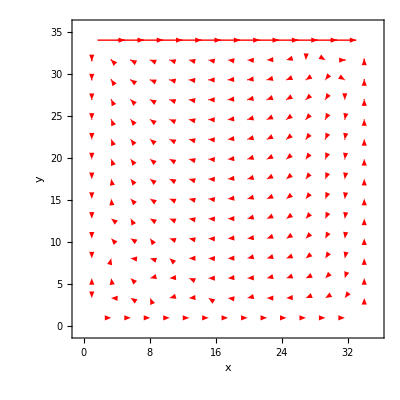

```mathematica
ListVectorPlot[VectorFormUV[RU[[6]],RV[[6]],imax,jmax],FrameLabel->{x,y},PerformanceGoal->"Speed",VectorStyle->Red]
```

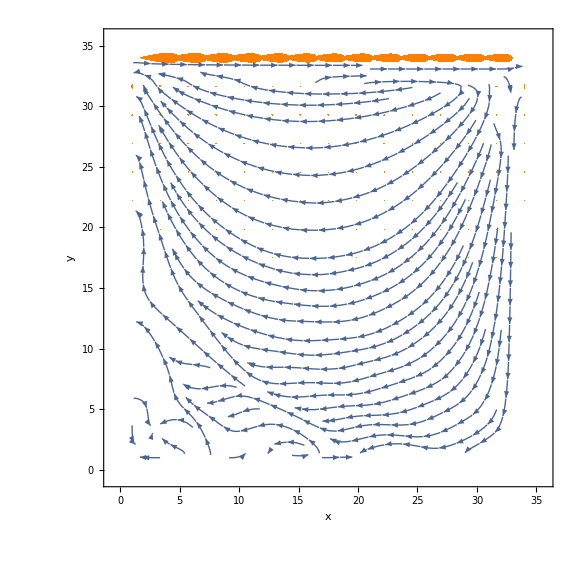

```mathematica
ListVectorPlot[VectorFormUV[RU[[6]],RV[[6]],imax,jmax],FrameLabel->{x,y},PerformanceGoal->"Quality",VectorStyle->{{Orange,"Drop"},{Green,"Dart"}},StreamPoints->45,StreamScale->Tiny,StreamScale->Tiny,AspectRatio->Automatic,PlotLegends->Automatic,ImageSize->Large]
```

```mathematica
gif=Table[ListVectorPlot[VectorFormUV[SU[[i]],SV[[i]],imax,jmax],FrameLabel->{x,y},PerformanceGoal->"Quality",VectorStyle->{{Orange,"Drop"},{Green,"Dart"}},StreamPoints->45,StreamScale->Tiny,ImageSize->Full],{i,1,Round[tend]}]; 
Export["labelsAnimate.mov",gif,ImageResolution->1080,Antialiasing->True,AnimationRate->.5,ImageSize->{1080,1080}]
```

labelsAnimate.mov

```mathematica
p="file-"<>DateString[Riffle[{"Year","Month","Day"},"-"]]<>".gif";
```

```mathematica
p
```

file-2020-04-26.gif